## Start

### Setup

#### Default options for plots, error messages, and colors

```mathematica
SetDirectory["/Users/gabrielpatenotte/Documents/Research/Ni Group/Mathematica"];
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{80,10},{80,10}},ImageSize->500,AxesLabel->{"",""},PlotStyle->Black]; 
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{80,10},{80,10}},ImageSize->500,AxesLabel->{"",""}]; 
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[ClebschGordan::phy]];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
colors=RGBColor/@{"#408EC6","#7A2048","#1E2761","#89ABE3FF","#EA738DFF","#8BB9B9"};
```

SetDirectory::cdir: Cannot set current directory to /Users/gabrielpatenotte/Documents/Research/Ni Group/Mathematica.

#### Basis labels

```mathematica
bUC={"I1","mI1","I2","mI2","N","mN","S","mS"};
bI={"I1","I2","I","mI","N","mN","S","mS"};
bJ={"I1","mI1","I2","mI2","N","S","J","mJ"};
bIJ={"I1","I2","I","mI","N","S","J","mJ"};
bF={"I1","I2","I","N","S","J","F","mF"};
bF1={"I1","I2","mI2","N","F1","mF1","S","J"};
bF2={"I1","mI1","I2","N","F2","mF2","S","J"};
bN={"N","mN"};
bI1={"I1","mI1"};
bI2={"I2","mI2"};
bS={"S","mS"};
b={bUC,bI,bJ,bIJ,bF,bF1,bF2,bN};
```

#### Supporting functions

```mathematica
conj[x_]:=Module[{re,im},x/.(Complex[re_,im_]->Complex[re,-im])]; (*Replacement that gives the complex conjugate*)
createSpace[aQN_Association]:=Module[{a},
a=Map[If[Length[#]==0,{#},#]&,aQN,1];
nℋ=Sum[(2I1+1)(2I2+1)(2N+1)(2S+1),{N,a["N"]},{S,a["S"]},{I1,a["I1"]},{I2,a["I2"]}]; (*number of states in Hilbert space*)
ℋ=IdentityMatrix[nℋ];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
nℋI1=(2a["I1"][[1]]+1);
nℋI2=(2a["I2"][[1]]+1);
nℋI=(2a["I1"][[1]]+1)(2a["I2"][[1]]+1);
nℋS=(2a["S"][[1]]+1);
nℋN=Sum[(2N+1),{N,a["N"]}];
ℋ=IdentityMatrix[nℋ];
ℋI1=IdentityMatrix[nℋI1];
ℋI2=IdentityMatrix[nℋI2];
ℋI=IdentityMatrix[nℋI];
ℋS=IdentityMatrix[nℋS];
ℋN=IdentityMatrix[nℋN];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
sℋI1=Partition[ℋI1,{nℋI1,1}][[1]];
sℋI2=Partition[ℋI2,{nℋI2,1}][[1]];
sℋI=Partition[ℋI,{nℋI,1}][[1]];
sℋS=Partition[ℋS,{nℋS,1}][[1]];
sℋN=Partition[ℋN,{nℋN,1}][[1]];
] (*example: aQN = Association["I1"->3/2, "I2"-> 7/2, "S"->0, "N"->{0,1}]*)
```

```mathematica
createLists[aQN_Association]:=Module[{a,spins},
a=Map[If[Length[#]==0,{#},#]&,aQN,1];
am={{I1,a["I1"]},{I2,a["I2"]},{S,a["S"]},{N,a["N"]}}; (*angular momentums*)
lUC=Flatten[Table[ToExpression[bUC],Evaluate[Sequence@@am],{mI1,-I1,I1},{mI2,-I2,I2},{mS,-S,S},{mN,-N,N}],7];
lI=Flatten[Table[ToExpression[bI],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{mI,-I,I},{mN,-N,N},{mS,-S,S}],7];
lJ=Flatten[Table[ToExpression[bJ],Evaluate[Sequence@@am],{mI1,-I1,I1},{mI2,-I2,I2},{J,Abs[N-S],N+S},{mJ,-J,J}],7];
lIJ=Flatten[Table[ToExpression[bIJ],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{mI,-I,I},{J,Abs[N-S],N+S},{mJ,-J,J}],7];
lF=Flatten[Table[ToExpression[bF],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{J,Abs[N-S],N+S},{F,Abs[I-J],I+J},{mF,-F,F}],7];
lF1=Flatten[Table[ToExpression[bF1],Evaluate[Sequence@@am],{mI2,-I2,I2},{J,Abs[N-S],N+S},{F1,Abs[I1-J],I1+J},{mF1,-F1,F1}],7];
lF2=Flatten[Table[ToExpression[bF2],Evaluate[Sequence@@am],{mI1,-I1,I1},{J,Abs[N-S],N+S},{F2,Abs[I2-J],I2+J},{mF2,-F2,F2}],7];
lN=Flatten[Table[ToExpression[bN],{N,a["N"]},{mN,-N,N}],1];
l = {lUC,lI,lJ,lIJ,lF,lF1,lF2,lN};
BtoL = AssociationThread[b->l];
LtoB = AssociationThread[l->b];
StoLN=AssociationThread[sℋN->lN];
LtoSN=AssociationThread[lN->sℋN];
yN=lN/.{n_,mn_}->SphericalHarmonicY[n,mn,θ,ϕ];
]
```

### Functions

```mathematica
eig[Hn_]:=Chop[Sort[Eigensystem[Hn]ᵀ]ᵀ];
reorder[list_,order_]:=Part[order,list];
VtoQN[eigenvector_,basis_:bUC,populationThreshold_:0.1]:=Module[{sS,sP},sS=SortBy[Select[eigenvector,Abs[#]^2>=populationThreshold&],Abs];
sP=Position[eigenvector,#][[1,1]]&/@sS;
Transpose@{Abs[#]^2&/@sS,BtoL[basis][[sP]]}]
QNtoS[rep_,basis_:bUC]:=With[{labels=rep[[All,1]],numbers=rep[[All,2]]},Flatten[Position[BtoL[basis][[All,Flatten[labels/.PositionIndex[basis]]]],numbers]]]
QNtoV[rep_,eigenvectors_,basis_:bUC]:=Module[{pos,eigs},pos=QNtoS[rep];eigs=OrderingBy[eigenvectors[[All,pos]],Total[Abs[#]^2]&][[-Length[pos];;-1]];eigs]
reduceV[vecs_,param_,s_,rep_]:=Module[{pos,l},
pos=Flatten[Position[bUC,#]&/@rep[[All,1]]];
l=Transpose@{lUC[[All,pos]],Abs[vecs[[param,s]]]^2};
l=Map[{#[[1,1]],Total[#[[All,2]]]}&,GatherBy[l,First]];
l[[All,2]]
]
```

### Load

```mathematica
aQN = Association["I1"->3/2, "I2"-> 7/2, "S"->0, "N"->Range[0,3]];
createSpace[aQN] (*creates a Hilbert space*)
createLists[aQN] (*creates a list of the quantum numbers of each basis state*)
lN=lN[[2;;]];
nℋN=nℋN-1;
HacN=Import["HacN.m"][[2;;Length[lN]+1,2;;Length[lN]+1]]; 
(*needs to be multiplied by U*)
```

### Hamiltonians

#### Rotational Hamiltonian

```mathematica
HN=DiagonalMatrix[(#(#+1)-2)&/@lN[[All,1]]]; (*needs to be multiplied by B*)
```

#### Interaction Hamiltonian

```mathematica
DME[{N_,M_},{Np_,Mp_},q_]:=(-1)^M √((2 N+1) (2 Np+1)) ThreeJSymbol[{N,-M},{1,q},{Np,Mp}] ThreeJSymbol[{N,0},{1,0},{Np,0}]
```

```mathematica
Dvec[{N_,M_},{Np_,Mp_}]:=Sum[(-1)^q{{1/(√2),-ⅈ/(√2),0},{0,0,1},{-1/(√2),-ⅈ/(√2),0}}[[q+2]]DME[{N,M},{Np,Mp},q],{q,-1,1}]
ℰ=Normalize[{2,5,3}]Cos[2π f t];
```

```mathematica
Hint=Table[Ω Dvec[lN[[i]],lN[[j]]].ℰ,{i,1,Length[lN]},{j,1,Length[lN]}];
```

```mathematica
νtab=Table[Switch[lN[[i,1]],0,f,1,0,2,f,3,2f],{i,nℋN}]
u=MatrixExp[-ⅈ 2π t DiagonalMatrix[νtab]];
```

{0,0,0,f,f,f,f,f,2 f,2 f,2 f,2 f,2 f,2 f,2 f}

```mathematica
consts={θh->1*(π/2-1/2 ArcCos[1/(√3)]),θq->π/2-ArcCos[1/(√3)],αpar->1872.1153,αperp->467.0375,U->5 10^6,B->3.4761/2 10^9};
H0=(2π B HN+2π U HacN/.consts);
```

```mathematica
HLF=H0+(Hint/.Ω->2π  10^7);
```

```mathematica
HRF=TrigToExp[ComplexExpand[u†.HLF.u-ⅈ u†.D[u,t]]];
```

```mathematica
Hrwa=.;Hrwa[f_]=HRF/.{Exp[x_]->0};
```

```mathematica
vals=(eig[H0][[1]])/(2π);vecs=eig[H0][[2]];
```

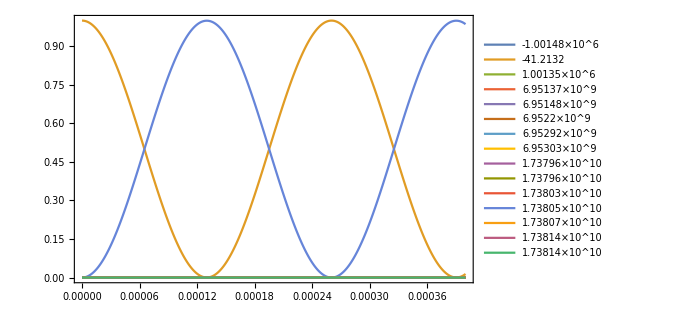

```mathematica
tS=0;tE=4 10^-4;tI=10^-6;
ListPlot[ParallelTable[(Abs[{eig[H0][[2,i]]}*.MatrixExp[-ⅈ Hrwa[(vals[[12]]-vals[[2]])/2-445] t].{eig[H0][[2,2]]}ᵀ]^2)[[1,1]],{i,1,nℋN},{t,Range[tS,tE,tI]}],Joined->True,PlotRange->{0,1},PlotLegends->Table[eig[H0/(2π)][[1,i]],{i,1,nℋN}],DataRange->{tS,tE}]
```

```mathematica
yN=yN[[2;;]]
```

{1/2 ⅇ^(-ⅈ ϕ) √(3/(2 π)) Sin[θ],1/2 √(3/π) Cos[θ],-1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ],1/4 ⅇ^(-2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2,1/2 ⅇ^(-ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ],1/4 √(5/π) (-1+3 Cos[θ]^2),-1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ],1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2,1/8 ⅇ^(-3 ⅈ ϕ) √(35/π) Sin[θ]^3,1/4 ⅇ^(-2 ⅈ ϕ) √(105/(2 π)) Cos[θ] Sin[θ]^2,1/8 ⅇ^(-ⅈ ϕ) √(21/π) (-1+5 Cos[θ]^2) Sin[θ],1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3),-1/8 ⅇ^(ⅈ ϕ) √(21/π) (-1+5 Cos[θ]^2) Sin[θ],1/4 ⅇ^(2 ⅈ ϕ) √(105/(2 π)) Cos[θ] Sin[θ]^2,-1/8 ⅇ^(3 ⅈ ϕ) √(35/π) Sin[θ]^3}

```mathematica
inst=eig[H0][[2]];
legend=Grid[Partition[Table[SphericalPlot3D[Abs[inst[[i]].yN]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All,AxesLabel->{"x","y","z"},ViewPoint->{0, 1, -2},ViewVertical->{0, 1,0},ImageSize->Tiny,Ticks->None,PlotStyle->ColorData[97,i]],{i,1,nℋN}],5]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

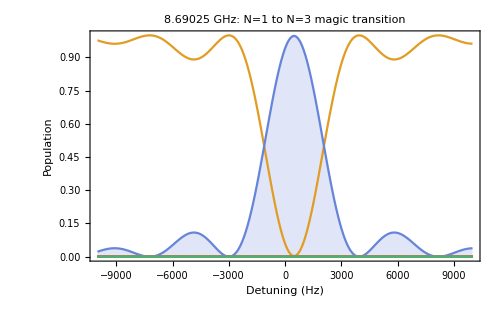

```mathematica
ListPlot[ParallelTable[(Abs[{eig[H0][[2,i]]}*.MatrixExp[-ⅈ Hrwa[(vals[[12]]-vals[[2]])/2-f] 0.000126].{eig[H0][[2,2]]}ᵀ]^2)[[1,1]],{i,1,nℋN},{f,Range[-10^4,10^4,10^2]}],Joined->True,PlotRange->{0,1},PlotLegends->legend,DataRange->{-10^4,10^4},Filling->{12->Axis},Frame->True,FrameLabel->{"Detuning (Hz)","Population"},ImagePadding->Automatic,PlotLabel->StringForm["`` GHz: N=1 to N=3 magic transition",(vals[[12]]-vals[[2]])/2(1/10^9)]]
```

# ND

```mathematica
vecs[[3]]
```

{0,1.,0,0,0,0,0,0,0,-0.0000172184,0,-0.0000565805,0,-0.0000172184,0}

```mathematica
H[t_]=HLF/.{f->(vals[[13]]-vals[[3]])/2};
ψ[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t],c9[t],c10[t],c11[t],c12[t],c13[t],c14[t],c15[t],c16[t]};init=ψ[0]==vecs[[3]];SE=ⅈ ψ'[t]== H[t].ψ[t];
sols=NDSolve[{SE,init},{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16},{t,10^-4},PrecisionGoal->8,Method->"StiffnessSwitching",MaxSteps->4000000];
```

Set::write: Tag List in {{0,2 π Cos[2 f π t],0},{2 π Cos[2 f π t],20 π,4 π Cos[2 f π t]},{0,4 π Cos[2 f π t],80 π}}[t_] is Protected.

NDSolve::deqn: Equation or list of equations expected instead of False in the first argument {{ⅈ c1'[t],ⅈ c2'[t],ⅈ c3'[t],ⅈ c4'[t],ⅈ c5'[t],ⅈ c6'[t],ⅈ c7'[t],ⅈ c8'[t],ⅈ c9'[t],ⅈ c10'[t],«6»}=={{0,2 π Cos[Times[«4»]],0},{2 π Cos[Times[«4»]],20 π,4 π Cos[Times[«4»]]},{0,4 π Cos[Times[«4»]],80 π}}[t].{c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t],c9[t],c10[t],«6»},False}.

```mathematica
ans=(Abs[(vecs[[13]].{c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t],c9[t],c10[t],c11[t],c12[t],c13[t],c14[t],c15[t],c16[t]})/.sols]^2)[[1]];
```

Dot::dotsh: Tensors {-0.0000330697,0,-0.0000330697,0,0,0,0,0,0.142669,0,«5»} and {c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t],c9[t],c10[t],«6»} have incompatible shapes.

ReplaceAll::reps: {NDSolve[{{ⅈ c1'[t],ⅈ c2'[t],ⅈ c3'[t],ⅈ c4'[t],ⅈ c5'[t],ⅈ c6'[t],ⅈ c7'[t],ⅈ c8'[t],ⅈ c9'[t],ⅈ c10'[t],«6»}=={{0,Times[«3»],0},{Times[«3»],Times[«2»],Times[«3»]},{0,Times[«3»],Times[«2»]}}[t].{c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t],c9[t],c10[t],«6»},False},{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,«6»},{t,1/10000},PrecisionGoal→8,Method→StiffnessSwitching,MaxSteps→4000000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Plot[ans,{t,0,10^-6}]
```

Dot::dotsh: Tensors {-0.0000330697,0,-0.0000330697,0,0,0,0,0,0.142669,0,«5»} and {c1[2.04286×10^-11],c2[2.04286×10^-11],c3[2.04286×10^-11],c4[2.04286×10^-11],c5[2.04286×10^-11],c6[2.04286×10^-11],c7[2.04286×10^-11],c8[2.04286×10^-11],c9[2.04286×10^-11],c10[2.04286×10^-11],«6»} have incompatible shapes.

NDSolve::dsvar: 2.04286×10^-11 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{ⅈ c1'[2.04286×10^-11],ⅈ c2'[2.04286×10^-11],ⅈ c3'[2.04286×10^-11],ⅈ c4'[2.04286×10^-11],ⅈ c5'[2.04286×10^-11],ⅈ c6'[2.04286×10^-11],ⅈ c7'[2.04286×10^-11],ⅈ c8'[2.04286×10^-11],ⅈ c9'[2.04286×10^-11],ⅈ c10'[2.04286×10^-11],«6»}=={{0,Times[«3»],0},{Times[«3»],Times[«2»],Times[«3»]},{0,Times[«3»],Times[«2»]}}[2.04286×10^-11].{c1[2.04286×10^-11],c2[2.04286×10^-11],c3[2.04286×10^-11],c4[2.04286×10^-11],«4»,c9[2.04286×10^-11],c10[2.04286×10^-11],«6»},False},«4»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Dot::dotsh: Tensors {-0.0000330697,0.,-0.0000330697,0.,0.,0.,0.,0.,0.142669,0.,«5»} and {c1[2.04286×10^-11],c2[2.04286×10^-11],c3[2.04286×10^-11],c4[2.04286×10^-11],c5[2.04286×10^-11],c6[2.04286×10^-11],c7[2.04286×10^-11],c8[2.04286×10^-11],c9[2.04286×10^-11],c10[2.04286×10^-11],«6»} have incompatible shapes.

NDSolve::ioppf: Value of option MaxSteps -> 4.×10^6 should be a positive integer or Infinity.

ReplaceAll::reps: {NDSolve[{{(0.+1. ⅈ) c1'[2.04286×10^-11],(0.+1. ⅈ) c2'[2.04286×10^-11],(0.+1. ⅈ) c3'[2.04286×10^-11],(0.+1. ⅈ) c4'[2.04286×10^-11],(0.+1. ⅈ) c5'[2.04286×10^-11],(0.+1. ⅈ) c6'[2.04286×10^-11],(0.+1. ⅈ) c7'[2.04286×10^-11],(0.+1. ⅈ) c8'[2.04286×10^-11],(0.+1. ⅈ) c9'[2.04286×10^-11],(0.+1. ⅈ) c10'[2.04286×10^-11],«6»}=={{0.,Times[«2»],0.},{Times[«2»],62.8319,Times[«2»]},{0.,Times[«2»],251.327}}[2.04286×10^-11].{c1[2.04286×10^-11],«9»,«6»},False},«4»,MaxSteps→4.×10^6]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Dot::dotsh: Tensors {-0.0000330697,0,-0.0000330697,0,0,0,0,0,0.142669,0,«5»} and {c1[2.04286×10^-8],c2[2.04286×10^-8],c3[2.04286×10^-8],c4[2.04286×10^-8],c5[2.04286×10^-8],c6[2.04286×10^-8],c7[2.04286×10^-8],c8[2.04286×10^-8],c9[2.04286×10^-8],c10[2.04286×10^-8],«6»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

NDSolve::dsvar: 2.04286×10^-8 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ioppf: Value of option MaxSteps -> 4.×10^6 should be a positive integer or Infinity.

NDSolve::dsvar: 4.08368×10^-8 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ioppf: Value of option MaxSteps -> 4.×10^6 should be a positive integer or Infinity.

General::stop: Further output of NDSolve::ioppf will be suppressed during this calculation.

-Graphics-

```mathematica
{p1,p2,p3,p4}=Abs[#[t 10^-6]/.sols]^2&/@{c1,c2,c3,c4};
```

NDSolve::deqn: Equation or list of equations expected instead of False in the first argument {{ⅈ c1'[t],ⅈ c2'[t],ⅈ c3'[t],ⅈ c4'[t],ⅈ c5'[t],ⅈ c6'[t],ⅈ c7'[t],ⅈ c8'[t],ⅈ c9'[t],ⅈ c10'[t],«6»}=={{0,2 π Cos[Times[«4»]],0},{2 π Cos[Times[«4»]],20 π,4 π Cos[Times[«4»]]},{0,4 π Cos[Times[«4»]],80 π}}[t].{c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t],c9[t],c10[t],«6»},False}.

ReplaceAll::reps: {NDSolve[{{ⅈ c1'[t],ⅈ c2'[t],ⅈ c3'[t],ⅈ c4'[t],ⅈ c5'[t],ⅈ c6'[t],ⅈ c7'[t],ⅈ c8'[t],ⅈ c9'[t],ⅈ c10'[t],«6»}=={{0,Times[«3»],0},{Times[«3»],Times[«2»],Times[«3»]},{0,Times[«3»],Times[«2»]}}[t].{c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t],c9[t],c10[t],«6»},False},{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,«6»},{t,1/10000},PrecisionGoal→8,Method→StiffnessSwitching,MaxSteps→4000000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Plot[{p1,p2,p4},{t,0,100},PlotStyle->Automatic]
```

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{ⅈ c1'[0.00204286],ⅈ c2'[0.00204286],ⅈ c3'[0.00204286],ⅈ c4'[0.00204286],ⅈ c5'[0.00204286],ⅈ c6'[0.00204286],ⅈ c7'[0.00204286],ⅈ c8'[0.00204286],ⅈ c9'[0.00204286],ⅈ c10'[0.00204286],«6»}=={{0,Times[«3»],0},{Times[«3»],Times[«2»],Times[«3»]},{0,Times[«3»],Times[«2»]}}[0.00204286].{c1[0.00204286],c2[0.00204286],c3[0.00204286],c4[0.00204286],«3»,c8[0.00204286],c9[0.00204286],c10[0.00204286],«6»},False},«4»,MaxSteps→4000000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ioppf: Value of option MaxSteps -> 4.×10^6 should be a positive integer or Infinity.

ReplaceAll::reps: {NDSolve[{{(0.+1. ⅈ) c1'[0.00204286],(0.+1. ⅈ) c2'[0.00204286],(0.+1. ⅈ) c3'[0.00204286],(0.+1. ⅈ) c4'[0.00204286],(0.+1. ⅈ) c5'[0.00204286],(0.+1. ⅈ) c6'[0.00204286],(0.+1. ⅈ) c7'[0.00204286],(0.+1. ⅈ) c8'[0.00204286],(0.+1. ⅈ) c9'[0.00204286],(0.+1. ⅈ) c10'[0.00204286],«6»}=={{0.,Times[«2»],0.},{Times[«2»],62.8319,Times[«2»]},{0.,Times[«2»],251.327}}[0.00204286].{c1[0.00204286],c2[0.00204286],«8»,«6»},False},{«1»},«2»,«1»,MaxSteps→4.×10^6]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{ⅈ c1'[2.04286],ⅈ c2'[2.04286],ⅈ c3'[2.04286],ⅈ c4'[2.04286],ⅈ c5'[2.04286],ⅈ c6'[2.04286],ⅈ c7'[2.04286],ⅈ c8'[2.04286],ⅈ c9'[2.04286],ⅈ c10'[2.04286],«6»}=={{0,Times[«3»],0},{Times[«3»],Times[«2»],Times[«3»]},{0,Times[«3»],Times[«2»]}}[2.04286].{c1[2.04286],c2[2.04286],c3[2.04286],c4[2.04286],c5[2.04286],c6[«19»],c7[2.04286],c8[2.04286],c9[2.04286],c10[2.04286],«6»},False},«5»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ioppf: Value of option MaxSteps -> 4.×10^6 should be a positive integer or Infinity.

NDSolve::dsvar: 4.08368 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ioppf: Value of option MaxSteps -> 4.×10^6 should be a positive integer or Infinity.

General::stop: Further output of NDSolve::ioppf will be suppressed during this calculation.

-Graphics-

```mathematica
vals[[3]]-vals[[1]]
```

2.00283×10^6

```mathematica
p2
```

NDSolve::deqn: Equation or list of equations expected instead of False in the first argument {{ⅈ c1'[t],ⅈ c2'[t],ⅈ c3'[t],ⅈ c4'[t],ⅈ c5'[t],ⅈ c6'[t],ⅈ c7'[t],ⅈ c8'[t],ⅈ c9'[t],ⅈ c10'[t],«6»}=={{0,2 π Cos[Times[«4»]],0},{2 π Cos[Times[«4»]],20 π,4 π Cos[Times[«4»]]},{0,4 π Cos[Times[«4»]],80 π}}[t].{c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t],c9[t],c10[t],«6»},False}.

ReplaceAll::reps: {NDSolve[{{ⅈ c1'[t],ⅈ c2'[t],ⅈ c3'[t],ⅈ c4'[t],ⅈ c5'[t],ⅈ c6'[t],ⅈ c7'[t],ⅈ c8'[t],ⅈ c9'[t],ⅈ c10'[t],«6»}=={{0,Times[«3»],0},{Times[«3»],Times[«2»],Times[«3»]},{0,Times[«3»],Times[«2»]}}[t].{c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t],c9[t],c10[t],«6»},False},{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,«6»},{t,1/10000},PrecisionGoal→8,Method→StiffnessSwitching,MaxSteps→4000000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Abs[c2[t/1000000]/.NDSolve[{{ⅈ c1'[t],ⅈ c2'[t],ⅈ c3'[t],ⅈ c4'[t],ⅈ c5'[t],ⅈ c6'[t],ⅈ c7'[t],ⅈ c8'[t],ⅈ c9'[t],ⅈ c10'[t],ⅈ c11'[t],ⅈ c12'[t],ⅈ c13'[t],ⅈ c14'[t],ⅈ c15'[t],ⅈ c16'[t]}=={{0,2 π Cos[2 f π t],0},{2 π Cos[2 f π t],20 π,4 π Cos[2 f π t]},{0,4 π Cos[2 f π t],80 π}}[t].{c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t],c9[t],c10[t],c11[t],c12[t],c13[t],c14[t],c15[t],c16[t]},False},{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16},{t,1/10000},PrecisionGoal→8,Method→StiffnessSwitching,MaxSteps→4000000]]^2

Set::write: Tag List in {{0,2 π Cos[2 f π t],0},{2 π Cos[2 f π t],20 π,4 π Cos[2 f π t]},{0,4 π Cos[2 f π t],80 π}}[t_] is Protected.

NDSolve::underdet: There are more dependent variables, {c1[t],c2[t],c3[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {NDSolve[{{ⅈ c1'[t],ⅈ c2'[t],ⅈ c3'[t]}=={{0,Times[«3»],0},{Times[«3»],Times[«2»],Times[«3»]},{0,Times[«3»],Times[«2»]}}[t].{c1[t],c2[t],c3[t]},{c1[0],c2[0],c3[0]}=={1,0,0}},{c1,c2,c3},{t,40},PrecisionGoal→8,Method→StiffnessSwitching,MaxSteps→40000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.000817143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{ⅈ c1'[0.000817143],ⅈ c2'[0.000817143],ⅈ c3'[0.000817143]}=={{0,Times[«3»],0},{Times[«3»],Times[«2»],Times[«3»]},{0,Times[«3»],Times[«2»]}}[0.000817143].{c1[0.000817143],c2[0.000817143],c3[0.000817143]},{c1[0],c2[0],c3[0]}=={1,0,0}},{c1,c2,c3},{0.000817143,40},PrecisionGoal→8,Method→StiffnessSwitching,MaxSteps→40000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ioppf: Value of option MaxSteps -> 40000. should be a positive integer or Infinity.

ReplaceAll::reps: {NDSolve[{{(0.+1. ⅈ) c1'[0.000817143],(0.+1. ⅈ) c2'[0.000817143],(0.+1. ⅈ) c3'[0.000817143]}=={{0.,Times[«2»],0.},{Times[«2»],62.8319,Times[«2»]},{0.,Times[«2»],251.327}}[0.000817143].{c1[0.000817143],c2[0.000817143],c3[0.000817143]},{c1[0.],c2[0.],c3[0.]}=={1.,0.,0.}},{c1,c2,c3},{0.000817143,40.},PrecisionGoal→8.,Method→StiffnessSwitching,MaxSteps→40000.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.817144 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{ⅈ c1'[0.817144],ⅈ c2'[0.817144],ⅈ c3'[0.817144]}=={{0,Times[«3»],0},{Times[«3»],Times[«2»],Times[«3»]},{0,Times[«3»],Times[«2»]}}[0.817144].{c1[0.817144],c2[0.817144],c3[0.817144]},{c1[0],c2[0],c3[0]}=={1,0,0}},{c1,c2,c3},{0.817144,40},PrecisionGoal→8,Method→StiffnessSwitching,MaxSteps→40000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ioppf: Value of option MaxSteps -> 40000. should be a positive integer or Infinity.

NDSolve::dsvar: 1.63347 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ioppf: Value of option MaxSteps -> 40000. should be a positive integer or Infinity.

General::stop: Further output of NDSolve::ioppf will be suppressed during this calculation.

-Graphics-

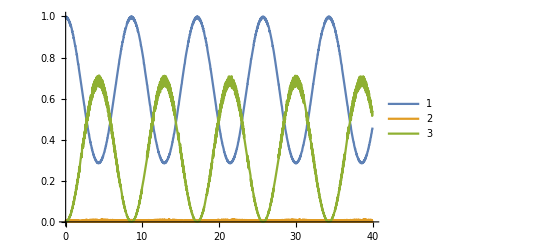

```mathematica
H[t_]=({{0, 2π Cos[2π f t], 0}, {2π Cos[2π f t], 2π 10, 4π Cos[2π f t]}, {0, 4π Cos[2π f t], 2π 40}})/.f->20.0;
ψ[t_]={c1[t],c2[t],c3[t]};init=ψ[0]=={1,0,0};SE=ⅈ ψ'[t]== H[t].ψ[t];
sols=NDSolve[{SE,init},{c1,c2,c3},{t,40},PrecisionGoal->8,Method->"StiffnessSwitching",MaxSteps->40000];
{p1,p2,p3}=Abs[#[t]/.sols]^2&/@{c1,c2,c3};
Plot[{p1,p2,p3},{t,0,40},PlotStyle->Automatic,PlotLegends->Automatic]
```

```mathematica
1/(1/(2π)(2π 4π)/(2π 10))//N
```

5.

```mathematica
H=({{0, 2π Cos[2π f t], 0}, {2π Cos[2π f t], 2π 10, 4π Cos[2π f t]}, {0, 4π Cos[2π f t], 2π 40}});
```

```mathematica
u=MatrixExp[-2π ⅈ t ({{0, 0, 0}, {0, f, 0}, {0, 0, 2f}})];
```

```mathematica
HRF=ComplexExpand[u†.H.u-ⅈ u†.D[u,t]];
```

```mathematica
Hrwa=TrigToExp[HRF]/.f->20/.Exp[x_]->0
```

{{0,π,0},{π,-20 π,2 π},{0,2 π,0}}

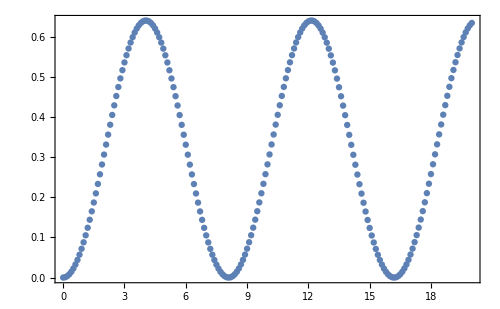

```mathematica
tab=ParallelTable[(Abs[({{0, 0, 1}}).MatrixExp[-ⅈ t Hrwa].({{1}, {0}, {0}})]^2)[[1,1]],{t,0,20,0.1}];
ListPlot[tab,DataRange->{0,20}]
```